```mathematica
M=5;
beta=0.1;
g=0.;
alpha=0.5;
l=0.9;
rz=0.5;
L=3.0;
epsilon=Exp[-2*L];
bVal[sigmaL_]=Tanh[sigmaL];
r[sigmaL_]=sigmaL*rz;

xi[z_,Delta_,OmegaA_,sign_]=M*(sign*Delta*z+OmegaA)

betaA=alpha+beta-1-xi^2

betaZ=Together[beta+2*alpha+2*alpha^2*(xi^4+2*g*xi^3+2*g^2*xi^2-5*xi^2-6*g*xi+3)/((xi^2-1)*(xi^4-6*xi^2-4*g*xi+3))]

nBetaZ=Numerator[betaZ]

dBetaZ=Denominator[betaZ]

q[z_,Delta_,OmegaA_]=((1-l)*nBetaZ+l*betaA*dBetaZ)/nBetaZ
F[z_,Delta_,OmegaA_]=(Sqrt[-q[z,Delta,OmegaA]/. xi->xi[z,Delta,OmegaA,1]]+Sqrt[-q[z,Delta,OmegaA]/. xi->xi[z,Delta,OmegaA,-1]])/(-z^2+1)
```

5 (OmegaA+Delta sign z)

-0.4-xi^2

(1.1 (-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6))/((-1.+xi^2) (3.-6. xi^2+xi^4))

1.1 (-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6)

(-1.+xi^2) (3.-6. xi^2+xi^4)

(0.909091 (0.9 (-0.4-xi^2) (-1.+xi^2) (3.-6. xi^2+xi^4)+0.11 (-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6)))/(-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6)

1/(1-z^2)(0.953463 √(-((0.9 (-0.4-25 (OmegaA-Delta z)^2) (-1.+25 (OmegaA-Delta z)^2) (3.-150. (OmegaA-Delta z)^2+625 (OmegaA-Delta z)^4)+0.11 (-1.63636+168.182 (OmegaA-Delta z)^2-4090.91 (OmegaA-Delta z)^4+15625. (OmegaA-Delta z)^6))/(-1.63636+168.182 (OmegaA-Delta z)^2-4090.91 (OmegaA-Delta z)^4+15625. (OmegaA-Delta z)^6)))+0.953463 √(-((0.9 (-0.4-25 (OmegaA+Delta z)^2) (-1.+25 (OmegaA+Delta z)^2) (3.-150. (OmegaA+Delta z)^2+625 (OmegaA+Delta z)^4)+0.11 (-1.63636+168.182 (OmegaA+Delta z)^2-4090.91 (OmegaA+Delta z)^4+15625. (OmegaA+Delta z)^6))/(-1.63636+168.182 (OmegaA+Delta z)^2-4090.91 (OmegaA+Delta z)^4+15625. (OmegaA+Delta z)^6))))

```mathematica
deltaValues=Range[0,1,0.01];
initialOmega=0.-0.12138250547239222 ⅈ;  (*Initial guess for the first Delta*)
sigmaLValues=Range[1,12,1]
omegaValues=Table[Table[initialOmega=OmegaA/. FindRoot[NIntegrate[F[z,Delta,OmegaA],{z,0,bVal[sigmaL]}]==r[sigmaL],{OmegaA,initialOmega}],{Delta,deltaValues}],{sigmaL,sigmaLValues}]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

NIntegrate::inumr: The integrand (1.90693 √(-(0.9 (-0.4-25 Power[«1»]) («1») (3.-150. Power[«2»]+625 Power[«2»])+«1»)/(-1.63636+168.182 («1»)^2-«18» «1»+15625. Plus[«2»]^6)))/(1-z^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,Tanh[1]}}.

NIntegrate::inumr: The integrand (0.953463 (-(0.9 (-0.4-25 Power[«2»]) («1») (-300. Plus[«2»]+2500 Power[«2»])+«4»)/(-1.63636+168.182 («1»)^2«1»«18»«1»«1»+15625. Plus[«2»]^6)+«1»))/(√(-(0.9 (-0.4-25 Power[«2»]) («1») (3.-150. Power[«2»]+625 Power[«2»])«1»«20»«1»(«1»«1»)/(-1.63636+168.182 (Plus«1»«1»])^2-«18» «1»+15625. Plus[«2»]^6)) (1-«1»)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,Tanh[1]}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.00369026}. NIntegrate obtained 0.510081-0.527935 ⅈ and 0.00769437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.0475937}. NIntegrate obtained 0.51138+8.56295 ⅈ and 0.00980416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.00526748}. NIntegrate obtained 0.509886+0.120364 ⅈ and 0.00139996 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{{-6.60804×10^-15-0.10363 ⅈ,-6.42011×10^-15-0.104297 ⅈ,-6.11578×10^-15-0.106057 ⅈ,-5.83577×10^-15-0.108554 ⅈ,-5.6022×10^-15-0.111566 ⅈ,-5.67175×10^-15-0.115642 ⅈ,-7.9885×10^-15-0.12199 ⅈ,-1.07726×10^-14-0.130616 ⅈ,-1.46225×10^-14-0.141973 ⅈ,-2.04756×10^-14-0.157067 ⅈ,-3.05353×10^-14-0.178104 ⅈ,-5.18146×10^-14-0.210814 ⅈ,-1.24477×10^-13-0.2781 ⅈ,-1.70667×10^-8-0.917913 ⅈ,-4.07272×10^-6-0.916578 ⅈ,-0.0000185514-0.915174 ⅈ,-0.00048482-0.913678 ⅈ,-0.000515121-0.913583 ⅈ,-0.000545422-0.913399 ⅈ,-0.000575724-0.913132 ⅈ,-0.000606025-0.912793 ⅈ,-0.000636326-0.912386 ⅈ,-0.000666627-0.911902 ⅈ,-0.000696929-0.911357 ⅈ,-0.00072723-0.910755 ⅈ,-0.000757531-0.910095 ⅈ,-0.000787832-0.909377 ⅈ,-0.000818134-0.908604 ⅈ,-0.000848435-0.907774 ⅈ,-0.000878736-0.90689 ⅈ,-0.000909037-0.905928 ⅈ,-0.000939338-0.904912 ⅈ,-0.00096964-0.903843 ⅈ,-0.000999941-0.902718 ⅈ,-0.00103024-0.901536 ⅈ,-0.00106054-0.900297 ⅈ,-0.00109084-0.898999 ⅈ,-0.00112115-0.897642 ⅈ,-0.00115145-0.89622 ⅈ,-0.00118175-0.894736 ⅈ,-0.00121205-0.893187 ⅈ,-0.00124235-0.891572 ⅈ,-0.00127265-0.889887 ⅈ,-0.00130295-0.888133 ⅈ,-0.00133325-0.886269 ⅈ,-0.00136356-0.884332 ⅈ,-0.00139386-0.882321 ⅈ,-0.00142416-0.880231 ⅈ,-0.00145446-0.87806 ⅈ,-0.00148476-0.875805 ⅈ,-0.00151506-0.87346 ⅈ,-0.00154536-0.871023 ⅈ,-0.00157566-0.86849 ⅈ,-0.00160597-0.865857 ⅈ,-0.00163627-0.863113 ⅈ,-0.00166657-0.860261 ⅈ,-0.00169687-0.857294 ⅈ,-0.00172717-0.854208 ⅈ,-0.00175747-0.850995 ⅈ,-0.00178777-0.847651 ⅈ,-0.00181807-0.844168 ⅈ,-0.00184838-0.840463 ⅈ,-0.00187868-0.83661 ⅈ,-0.00190898-0.832602 ⅈ,0.00193928-0.692867 ⅈ,0.00196958-0.692763 ⅈ,0.00199988-0.692511 ⅈ,0.00203018-0.692107 ⅈ,0.00206048-0.691538 ⅈ,0.00209079-0.690798 ⅈ,0.00212109-0.689868 ⅈ,0.00215139-0.688745 ⅈ,0.00218169-0.687415 ⅈ,0.00221199-0.685865 ⅈ,0.00224229-0.684057 ⅈ,0.00227259-0.681995 ⅈ,0.00135641-0.570637 ⅈ,0.0023332-0.564306 ⅈ,0.0023635-0.564096 ⅈ,0.0023938-0.563708 ⅈ,0.0024241-0.563134 ⅈ,0.0024544-0.562351 ⅈ,0.0024847-0.561354 ⅈ,0.002515-0.560125 ⅈ,0.00229416-0.474931 ⅈ,0.00229416-0.474931 ⅈ,-0.00225465-0.45434 ⅈ,-0.00225465-0.45434 ⅈ,0.00240073-0.433923 ⅈ,0.00240073-0.433923 ⅈ,-0.00205079-0.416689 ⅈ,-0.00205079-0.416689 ⅈ,0.0014678-0.394303 ⅈ,0.0014678-0.394303 ⅈ,-0.00246101-0.383225 ⅈ,-0.00246101-0.383225 ⅈ,-0.00246101-0.383225 ⅈ,0.00285235-0.373199 ⅈ,0.00282491-0.367466 ⅈ,0.00280393-0.362432 ⅈ,0.00278525-0.35799 ⅈ},{-3.7082×10^-16-0.10363 ⅈ,-3.53828×10^-16-0.105064 ⅈ,-3.34892×10^-16-0.108772 ⅈ,-3.27004×10^-16-0.114184 ⅈ,-5.46843×10^-16-0.123908 ⅈ,-8.29507×10^-16-0.138947 ⅈ,-1.34684×10^-15-0.161762 ⅈ,-2.59896×10^-15-0.200706 ⅈ,-1.00428×10^-14-0.309197 ⅈ,-3.39124×10^-7-0.918373 ⅈ,-0.0000102359-0.916544 ⅈ,-0.0000199974-0.914672 ⅈ,-0.000460264-0.912381 ⅈ,-0.00049862-0.91219 ⅈ,-0.000536975-0.911828 ⅈ,-0.000575331-0.911304 ⅈ,-0.000613686-0.910649 ⅈ,-0.000652041-0.909867 ⅈ,-0.000690397-0.908929 ⅈ,-0.000728752-0.90788 ⅈ,-0.000767108-0.906721 ⅈ,-0.000805463-0.905448 ⅈ,-0.000843818-0.904063 ⅈ,-0.000882174-0.902557 ⅈ,-0.000920529-0.900934 ⅈ,-0.000958884-0.899189 ⅈ,-0.00099724-0.897265 ⅈ,-0.0010356-0.895219 ⅈ,-0.00107395-0.893044 ⅈ,-0.00111231-0.89073 ⅈ,-0.00115066-0.888274 ⅈ,-0.00118902-0.885666 ⅈ,-0.00122737-0.882888 ⅈ,-0.00126573-0.879941 ⅈ,-0.00130408-0.876812 ⅈ,-0.00134244-0.873487 ⅈ,-0.00138079-0.869954 ⅈ,-0.00141915-0.866098 ⅈ,-0.0014575-0.86201 ⅈ,-0.00149586-0.857668 ⅈ,0.00153422-0.743923 ⅈ,0.00157257-0.743705 ⅈ,0.00161093-0.743172 ⅈ,0.00164928-0.74229 ⅈ,0.00168764-0.741045 ⅈ,0.00172599-0.739394 ⅈ,0.00176435-0.737264 ⅈ,-0.0018027-0.630368 ⅈ,-0.0018027-0.630368 ⅈ,-0.00187941-0.629525 ⅈ,-0.00191777-0.628609 ⅈ,-0.00195612-0.627089 ⅈ,-0.00199448-0.548818 ⅈ,-0.00203284-0.547942 ⅈ,-0.00167192-0.473753 ⅈ,-0.00202832-0.438648 ⅈ,0.00138842-0.393334 ⅈ,0.00133462-0.363962 ⅈ,0.00129905-0.332463 ⅈ,0.00127536-0.307773 ⅈ,-0.00200352-0.286497 ⅈ,-0.0014492-0.26743 ⅈ,-0.00132413-0.261229 ⅈ,-0.00123828-0.250372 ⅈ,-0.00122673-0.242567 ⅈ,-0.00123656-0.236374 ⅈ,-0.00123878-0.231341 ⅈ,-0.00124048-0.227453 ⅈ,-0.00124732-0.224513 ⅈ,-0.00125503-0.222345 ⅈ,-0.00125782-0.220879 ⅈ,-0.00125959-0.219533 ⅈ,-0.00126235-0.218889 ⅈ,-0.0012649-0.218294 ⅈ,-0.0012649-0.218294 ⅈ,-0.0012649-0.218294 ⅈ,-0.0012649-0.218294 ⅈ,-0.0012649-0.218294 ⅈ,-0.0012649-0.218294 ⅈ,-0.0012649-0.218294 ⅈ,-0.0012649-0.218294 ⅈ,-0.00126995-0.218889 ⅈ,-0.00127568-0.219529 ⅈ,-0.00128208-0.220211 ⅈ,-0.0012866-0.220947 ⅈ,-0.00129128-0.22171 ⅈ,-0.00129364-0.222511 ⅈ,-0.00129915-0.223352 ⅈ,-0.00130383-0.224198 ⅈ,0.00339829-0.225069 ⅈ,0.00339829-0.225069 ⅈ,0.00339829-0.225069 ⅈ,0.00339829-0.225069 ⅈ,0.00339829-0.225069 ⅈ,0.00339829-0.225069 ⅈ,0.00299065-0.228388 ⅈ,0.00299065-0.228388 ⅈ,0.00292384-0.230608 ⅈ,0.00292384-0.230608 ⅈ,0.00287859-0.232521 ⅈ,0.00287859-0.232521 ⅈ},{-2.42038×10^-10-0.10363 ⅈ,-2.29877×10^-10-0.105498 ⅈ,-2.20166×10^-10-0.110437 ⅈ,-2.33332×10^-10-0.118887 ⅈ,-3.63738×10^-10-0.1338 ⅈ,-6.0827×10^-10-0.157593 ⅈ,-1.26117×10^-9-0.200275 ⅈ,-7.39599×10^-9-0.352711 ⅈ,-7.46796×10^-6-0.918731 ⅈ,-0.000356309-0.916723 ⅈ,-0.000395898-0.916485 ⅈ,-0.000435488-0.916068 ⅈ,-0.000475078-0.915472 ⅈ,-0.000514668-0.914731 ⅈ,-0.000554258-0.913857 ⅈ,-0.000593848-0.912815 ⅈ,-0.000633438-0.911653 ⅈ,-0.000673027-0.91037 ⅈ,-0.000712617-0.908957 ⅈ,-0.000752207-0.90742 ⅈ,-0.000791797-0.905754 ⅈ,-0.000831387-0.903887 ⅈ,-0.000870977-0.901892 ⅈ,-0.000910566-0.89976 ⅈ,-0.000950156-0.897484 ⅈ,-0.000989746-0.895051 ⅈ,-0.00102934-0.892453 ⅈ,-0.00106893-0.88967 ⅈ,-0.00110852-0.8867 ⅈ,-0.00114811-0.883528 ⅈ,-0.0011877-0.880135 ⅈ,-0.00122729-0.876393 ⅈ,-0.00126688-0.791757 ⅈ,-0.00130646-0.791408 ⅈ,-0.00134605-0.790706 ⅈ,-0.00138564-0.789622 ⅈ,-0.00142523-0.788141 ⅈ,-0.00146482-0.786192 ⅈ,0.00150441-0.725042 ⅈ,0.001544-0.724369 ⅈ,0.00158359-0.723184 ⅈ,-0.00162318-0.681934 ⅈ,-0.00166277-0.680879 ⅈ,0.00157844-0.618641 ⅈ,0.00174195-0.615724 ⅈ,-0.00141184-0.556508 ⅈ,0.00180513-0.508092 ⅈ,-0.00163122-0.413888 ⅈ,-0.00127355-0.334633 ⅈ,-0.000342745-2.69501×10^-15 ⅈ,-0.000349584+8.35867×10^-7 ⅈ,-0.000349802-2.1531×10^-15 ⅈ,-0.000330378-8.34069×10^-16 ⅈ,-0.000330378-8.34069×10^-16 ⅈ,-0.000330378+1.21461×10^-15 ⅈ,-0.000330378+1.21461×10^-15 ⅈ,0.000562582-0.0000409907 ⅈ,0.000539453+3.13475×10^-15 ⅈ,0.000539453-1.44058×10^-15 ⅈ,0.00042022+4.60464×10^-7 ⅈ,0.000422396-4.74997×10^-6 ⅈ,0.00113377-1.76207×10^-15 ⅈ,0.00113841+1.61334×10^-15 ⅈ,0.00113841+1.61334×10^-15 ⅈ,0.00113841+1.61334×10^-15 ⅈ,0.00113841-1.92081×10^-15 ⅈ,0.00112667-1.63657×10^-8 ⅈ,0.000865776+0.156333 ⅈ,0.00127434+0.157951 ⅈ,-0.000701102+0.15993 ⅈ,-0.00134273+0.161764 ⅈ,-0.00137538+0.163744 ⅈ,-0.00137471+0.1657 ⅈ,-0.00138589+0.167541 ⅈ,-0.00139713+0.169468 ⅈ,-0.00139716+0.171338 ⅈ,-0.00138417+0.173187 ⅈ,-0.00138057+0.175021 ⅈ,-0.00137947+0.176829 ⅈ,-0.00137253+0.178611 ⅈ,-0.001373+0.180372 ⅈ,-0.00136404+0.1821 ⅈ,-0.00136539+0.183809 ⅈ,-0.00137854+0.185432 ⅈ,-0.00136682+0.187114 ⅈ,-0.00137019+0.188754 ⅈ,-0.00136725+0.19035 ⅈ,-0.00135799+0.191916 ⅈ,-0.00136558+0.193468 ⅈ,0.00304248+0.194986 ⅈ,0.00302065+0.196527 ⅈ,0.00302065+0.196527 ⅈ,0.00302065+0.196527 ⅈ,0.00280019+0.200207 ⅈ,0.00280019+0.200207 ⅈ,0.00277592+0.202972 ⅈ,0.00277592+0.202972 ⅈ,0.00276031+0.205614 ⅈ,0.00276031+0.205614 ⅈ,0.00275593+0.208159 ⅈ,0.00275593+0.208159 ⅈ},{-8.22068×10^-12+0.10363 ⅈ,-7.80035×10^-12+0.105748 ⅈ,-7.57813×10^-12+0.111483 ⅈ,-8.46017×10^-12+0.122023 ⅈ,-1.34189×10^-11+0.140238 ⅈ,-2.44635×10^-11+0.170699 ⅈ,-6.60549×10^-11+0.236366 ⅈ,0.000278319-0.919988 ⅈ,0.000318079-0.919728 ⅈ,0.000357839-0.919257 ⅈ,0.000397599-0.918646 ⅈ,0.000437359-0.917896 ⅈ,0.000477119-0.917019 ⅈ,0.000516879-0.915974 ⅈ,0.000556639-0.914817 ⅈ,0.000596399-0.913542 ⅈ,0.000636159-0.91214 ⅈ,0.000675919-0.910618 ⅈ,0.000715678-0.908967 ⅈ,0.000755438-0.907185 ⅈ,0.000795198-0.905198 ⅈ,0.000834958-0.903076 ⅈ,0.000874718-0.900809 ⅈ,0.000914478-0.898383 ⅈ,0.000954238-0.895791 ⅈ,0.000993998-0.89301 ⅈ,0.00103376-0.890037 ⅈ,0.00107352-0.886856 ⅈ,-0.00111328-0.817151 ⅈ,-0.00115304-0.81681 ⅈ,-0.0011928-0.816116 ⅈ,-0.00123256-0.815047 ⅈ,-0.00127232-0.813596 ⅈ,-0.00131208-0.811696 ⅈ,0.00135184-0.754379 ⅈ,0.0013916-0.753822 ⅈ,0.00143136-0.752776 ⅈ,-0.00147112-0.721468 ⅈ,-0.00151088-0.720378 ⅈ,0.00155064-0.663587 ⅈ,0.0015904-0.662961 ⅈ,-0.000256385-0.611788 ⅈ,-0.00166992-0.585319 ⅈ,0.000159091-0.524176 ⅈ,0.00122518+0.257132 ⅈ,1.14696×10^-6+0.232247 ⅈ,0.00123669+0.215753 ⅈ,0.0012082+0.201974 ⅈ,-0.00123356+0.187322 ⅈ,0.0015041+0.170887 ⅈ,0.00068312+0.154527 ⅈ,-0.0403534+0.0000266031 ⅈ,-0.0403701-1.75443×10^-15 ⅈ,-0.0403701-1.75443×10^-15 ⅈ,-0.0673425+0.0000206932 ⅈ,-0.0672331-7.71036×10^-7 ⅈ,-0.0672291+3.29859×10^-6 ⅈ,-0.100832+8.71459×10^-8 ⅈ,-0.105536-8.89906×10^-6 ⅈ,-0.105533-0.0000177895 ⅈ,-0.105566-0.0000274489 ⅈ,-0.137489-0.0000257362 ⅈ,-0.136633+0.0000515384 ⅈ,-0.140862-0.000059418 ⅈ,-0.168404+0.0000470296 ⅈ,-0.174645+0.0000764111 ⅈ,-0.188203+2.97359×10^-6 ⅈ,-0.188204+3.57661×10^-15 ⅈ,-0.188204-1.95032×10^-15 ⅈ,-0.188204-1.95032×10^-15 ⅈ,-0.191457-0.0000744035 ⅈ,-0.191524-2.45164×10^-9 ⅈ,-0.191524-3.09971×10^-12 ⅈ,-0.191558+3.12753×10^-6 ⅈ,-0.00113063-0.149827 ⅈ,-0.00135982-0.15295 ⅈ,-0.00135982-0.15295 ⅈ,0.00137732-0.156527 ⅈ,0.00150324-0.158768 ⅈ,0.00150324-0.158768 ⅈ,-0.00146282-0.162187 ⅈ,-0.00130326-0.164865 ⅈ,-0.00143674-0.166268 ⅈ,-0.00144766-0.168355 ⅈ,-0.00148214-0.170125 ⅈ,-0.00146314-0.171974 ⅈ,-0.00146314-0.171974 ⅈ,0.00167924-0.175112 ⅈ,0.00167924-0.175112 ⅈ,0.00140209-0.178707 ⅈ,0.00141471-0.18037 ⅈ,0.00144034-0.182014 ⅈ,0.00142767-0.183593 ⅈ,0.00144095-0.18513 ⅈ,0.0014398-0.186674 ⅈ,0.0014398-0.186674 ⅈ,0.00270226-0.191246 ⅈ,0.00270226-0.191246 ⅈ,0.00270226-0.191246 ⅈ,0.00277427-0.19368 ⅈ,0.00277427-0.19368 ⅈ},{3.40232×10^-14-0.10363 ⅈ,3.22868×10^-14-0.105906 ⅈ,3.1771×10^-14-0.112194 ⅈ,3.6793×10^-14-0.124131 ⅈ,5.95683×10^-14-0.14459 ⅈ,1.16257×10^-13-0.180225 ⅈ,4.1674×10^-13-0.272983 ⅈ,3.91174×10^-11-0.91976 ⅈ,1.53673×10^-10-0.917728 ⅈ,5.62613×10^-10-0.915547 ⅈ,1.09561×10^-9-0.913221 ⅈ,1.38063×10^-8-0.91031 ⅈ,1.52031×10^-7-0.907451 ⅈ,7.155×10^-7-0.90409 ⅈ,3.32283×10^-6-0.900455 ⅈ,0.0000160607-0.896366 ⅈ,0.000636528-0.892194 ⅈ,0.000676311-0.891909 ⅈ,0.000716094-0.891356 ⅈ,0.000755877-0.890564 ⅈ,0.00079566-0.889511 ⅈ,0.000835443-0.888232 ⅈ,0.000875226-0.886724 ⅈ,0.000915009-0.884987 ⅈ,0.000954792-0.882961 ⅈ,0.000994575-0.8807 ⅈ,0.00103436-0.878191 ⅈ,-0.00107414-0.82019 ⅈ,-0.00111392-0.819852 ⅈ,-0.00115371-0.819147 ⅈ,-0.00119349-0.818052 ⅈ,-0.00123327-0.816559 ⅈ,-0.00127306-0.765853 ⅈ,-0.00131284-0.765448 ⅈ,-0.00135262-0.764556 ⅈ,0.0013924-0.735474 ⅈ,0.00143219-0.734524 ⅈ,-0.00147197-0.68661 ⅈ,-0.00151175-0.685956 ⅈ,0.00155154-0.638055 ⅈ,0.00159132-0.637183 ⅈ,0.0016311-0.581144 ⅈ,-0.00124779+0.223747 ⅈ,-0.0016728+0.210045 ⅈ,0.237882+2.45303×10^-15 ⅈ,0.237882+2.45303×10^-15 ⅈ,0.237881+2.11586×10^-15 ⅈ,0.268044+4.23224×10^-6 ⅈ,0.26805-9.87171×10^-9 ⅈ,0.287934-1.77038×10^-15 ⅈ,0.287934-1.77038×10^-15 ⅈ,0.307869-5.50104×10^-14 ⅈ,0.307887+3.79361×10^-8 ⅈ,0.307887+7.68897×10^-14 ⅈ,0.307899-1.89852×10^-15 ⅈ,0.348064-2.7264×10^-15 ⅈ,0.348064-2.7264×10^-15 ⅈ,0.348064-2.7264×10^-15 ⅈ,0.348064-2.7264×10^-15 ⅈ,0.00651055+0.0000354514 ⅈ,0.0064981-1.41487×10^-15 ⅈ,0.00626615-9.17522×10^-14 ⅈ,0.00607342+2.35267×10^-15 ⅈ,0.00607342+2.35267×10^-15 ⅈ,0.00607342-2.29059×10^-15 ⅈ,0.00607342-2.29059×10^-15 ⅈ,0.055249+2.61817×10^-15 ⅈ,0.055249+8.89879×10^-16 ⅈ,0.0549362-1.58253×10^-6 ⅈ,0.0549362-2.18009×10^-15 ⅈ,0.0549362-2.18009×10^-15 ⅈ,-0.000633933+0.132132 ⅈ,5.09154×10^-7+0.134078 ⅈ,3.01166×10^-9+0.136221 ⅈ,-1.75264×10^-9+0.138294 ⅈ,-3.16034×10^-11+0.140404 ⅈ,6.39581×10^-11+0.142475 ⅈ,8.86376×10^-12+0.14455 ⅈ,-1.85927×10^-11+0.146617 ⅈ,-1.71034×10^-11+0.148612 ⅈ,-6.34493×10^-12+0.150611 ⅈ,2.86921×10^-12+0.152527 ⅈ,-2.38374×10^-11+0.154534 ⅈ,-1.3287×10^-10+0.156369 ⅈ,1.52905×10^-10+0.158295 ⅈ,4.14138×10^-11+0.160092 ⅈ,-1.51255×10^-10+0.161937 ⅈ,-4.21332×10^-10+0.163697 ⅈ,2.06192×10^-9+0.16546 ⅈ,-1.61428×10^-8+0.167225 ⅈ,2.29119×10^-7+0.168993 ⅈ,-7.0287×10^-7+0.170576 ⅈ,2.55809×10^-6+0.172254 ⅈ,0.0000274231+0.173985 ⅈ,0.00159665+0.17404 ⅈ,-0.00161923+0.176786 ⅈ,-0.00161923+0.176786 ⅈ,0.0018402+0.179846 ⅈ,0.0018402+0.179846 ⅈ,0.0026577+0.183036 ⅈ,0.0026577+0.183036 ⅈ},{-5.5722×10^-10+0.10363 ⅈ,-5.28983×10^-10+0.106015 ⅈ,-5.26183×10^-10+0.112711 ⅈ,-7.70618×10^-10+0.125622 ⅈ,-1.27009×10^-9+0.147702 ⅈ,-2.6165×10^-9+0.187465 ⅈ,-1.29328×10^-8+0.313893 ⅈ,-0.000278503+0.921842 ⅈ,-0.000318289+0.921253 ⅈ,-0.000358075+0.920537 ⅈ,-0.000397861+0.919704 ⅈ,-0.000437647+0.918702 ⅈ,-0.000477433+0.917598 ⅈ,-0.000517219+0.916383 ⅈ,-0.000557006+0.915056 ⅈ,-0.000596792+0.913605 ⅈ,-0.000636578+0.912031 ⅈ,-0.000676364+0.910328 ⅈ,-0.00071615+0.908414 ⅈ,-0.000755936+0.906371 ⅈ,-0.000795722+0.904186 ⅈ,-0.000835508+0.901847 ⅈ,-0.000875294+0.899344 ⅈ,0.0278727+1.88145×10^-15 ⅈ,0.0278727+1.88145×10^-15 ⅈ,0.0278727+1.88145×10^-15 ⅈ,0.0278727+1.88145×10^-15 ⅈ,0.0682002-2.50952×10^-15 ⅈ,0.0682002-2.50952×10^-15 ⅈ,0.0882706-5.7478×10^-14 ⅈ,0.0883204+3.21101×10^-8 ⅈ,0.107985+1.35776×10^-8 ⅈ,0.11804-1.93347×10^-15 ⅈ,0.118094-1.25449×10^-9 ⅈ,-0.00135273-0.730514 ⅈ,-0.00139251-0.729991 ⅈ,0.0014323-0.699334 ⅈ,0.00147209-0.698546 ⅈ,-0.00151187-0.648282 ⅈ,-0.00155166-0.647391 ⅈ,-0.00118721-0.207105 ⅈ,0.00132336-0.202726 ⅈ,-0.00129459-0.196605 ⅈ,-0.00125527-0.190185 ⅈ,-0.00117504-0.182589 ⅈ,0.00123261-0.173669 ⅈ,0.0017762-0.16365 ⅈ,0.000612305-0.147667 ⅈ,-0.0130185+4.15435×10^-14 ⅈ,-0.0130185+4.15435×10^-14 ⅈ,-0.0130185+2.34185×10^-15 ⅈ,-0.0130185+2.34185×10^-15 ⅈ,-0.0134568+2.26202×10^-15 ⅈ,-0.0630415+1.16228×10^-15 ⅈ,-0.072959-6.32365×10^-11 ⅈ,-0.0830506+1.49499×10^-15 ⅈ,-0.09303-2.37905×10^-15 ⅈ,-0.103065+1.7428×10^-15 ⅈ,-0.113025-1.27811×10^-15 ⅈ,-0.113025-1.27811×10^-15 ⅈ,-0.133048+5.15742×10^-6 ⅈ,-0.143063-1.3096×10^-15 ⅈ,-0.143063-1.3096×10^-15 ⅈ,-0.163101+2.47062×10^-15 ⅈ,-0.173078+7.82517×10^-10 ⅈ,-0.183052-4.32119×10^-10 ⅈ,-0.183052-1.01257×10^-11 ⅈ,-0.183052-1.68718×10^-15 ⅈ,-0.183063-2.22487×10^-6 ⅈ,-0.223101+2.1835×10^-13 ⅈ,-0.233125+2.88254×10^-6 ⅈ,-0.243064-7.0211×10^-9 ⅈ,-0.253038+2.75974×10^-7 ⅈ,-0.262972-5.97495×10^-13 ⅈ,-0.273063+0.000022641 ⅈ,-0.283055+4.28137×10^-7 ⅈ,-0.29313+0.0000544169 ⅈ,-0.30302+4.35068×10^-15 ⅈ,-0.313112+5.18199×10^-10 ⅈ,-0.323063+2.82541×10^-15 ⅈ,-0.332879-0.0000297646 ⅈ,-0.333275+0.000052187 ⅈ,-0.333399+0.0000175904 ⅈ,-0.36306+3.14347×10^-9 ⅈ,-0.363073-0.0000464518 ⅈ,-0.383065+4.0267×10^-7 ⅈ,-0.383066-2.65099×10^-15 ⅈ,-0.383064+0.0000168579 ⅈ,-0.413047-1.28779×10^-6 ⅈ,-0.413112-3.32955×10^-15 ⅈ,-0.433055-7.49984×10^-7 ⅈ,-0.433055+1.76113×10^-15 ⅈ,-0.453049+4.0649×10^-9 ⅈ,-0.463014-1.71382×10^-15 ⅈ,-0.463014-1.71382×10^-15 ⅈ,-0.483014+7.04064×10^-6 ⅈ,-0.492857-5.69305×10^-9 ⅈ,-0.503008+1.5853×10^-7 ⅈ,-0.513097-2.13637×10^-15 ⅈ,-0.513131-1.5494×10^-7 ⅈ,-0.513131+1.75177×10^-15 ⅈ},{-0.203733-1.32427×10^-15 ⅈ,-0.211498-0.0000201022 ⅈ,-0.219922+1.76724×10^-9 ⅈ,-0.228522+1.69761×10^-15 ⅈ,-0.238549-7.07136×10^-12 ⅈ,-0.248318-1.35823×10^-13 ⅈ,-0.256308-1.05783×10^-11 ⅈ,-0.267968+1.8799×10^-15 ⅈ,-0.274946+3.11208×10^-15 ⅈ,-0.287319-2.26119×10^-15 ⅈ,-0.287319-2.26119×10^-15 ⅈ,-0.287319-2.26119×10^-15 ⅈ,0.000477438+0.907778 ⅈ,0.000517225+0.907393 ⅈ,0.000557011+0.906764 ⅈ,0.000596798+0.905928 ⅈ,0.000636585+0.90486 ⅈ,0.000676371+0.903608 ⅈ,0.000716158+0.902167 ⅈ,0.000755944+0.900541 ⅈ,0.000795731+0.898659 ⅈ,0.000835517+0.896597 ⅈ,-0.0180042-1.8605×10^-15 ⅈ,-0.0180054+4.33251×10^-6 ⅈ,-0.0180054+4.33847×10^-6 ⅈ,-0.0180054+4.33847×10^-6 ⅈ,-0.0180054+4.33847×10^-6 ⅈ,-0.0180045-5.80127×10^-6 ⅈ,-0.0180042-4.52274×10^-6 ⅈ,-0.088442+2.87932×10^-6 ⅈ,-0.0985105-5.99901×10^-9 ⅈ,-0.0985105+1.59773×10^-15 ⅈ,-0.0985105+1.59773×10^-15 ⅈ,-0.103921+3.62837×10^-12 ⅈ,-0.13801-2.50645×10^-8 ⅈ,-0.138005+0.0000129146 ⅈ,-0.137999-1.75037×10^-15 ⅈ,-0.137999-1.75037×10^-15 ⅈ,-0.178281-7.77235×10^-11 ⅈ,-0.178281+1.56847×10^-15 ⅈ,-0.19842-1.16611×10^-8 ⅈ,-0.208498-7.18805×10^-6 ⅈ,-0.208508-5.05713×10^-7 ⅈ,-0.228593+0.0000224566 ⅈ,-0.228565+1.53867×10^-10 ⅈ,-0.248304+1.86499×10^-15 ⅈ,-0.248304+1.86499×10^-15 ⅈ,-0.268854-1.19253×10^-11 ⅈ,-0.278667-0.0000133762 ⅈ,-0.27866-5.1117×10^-8 ⅈ,-0.278661-1.77139×10^-8 ⅈ,-0.308641+1.8264×10^-8 ⅈ,-0.31882+9.16447×10^-10 ⅈ,-0.31882+6.52816×10^-13 ⅈ,-0.31882-1.77103×10^-15 ⅈ,-0.31882+9.13676×10^-16 ⅈ,-0.318821-3.13357×10^-8 ⅈ,-0.368548+0.0000418809 ⅈ,-0.378524+4.83131×10^-9 ⅈ,-0.388622+5.79602×10^-6 ⅈ,-0.400205-0.000010089 ⅈ,-0.400236+3.70951×10^-10 ⅈ,-0.418505+0.0000192944 ⅈ,-0.428446+5.40521×10^-9 ⅈ,-0.438756-8.51928×10^-6 ⅈ,-0.448544-1.30187×10^-11 ⅈ,-0.458861-3.25986×10^-6 ⅈ,-0.468831-4.01788×10^-6 ⅈ,-0.468843-1.72556×10^-7 ⅈ,-0.48878+1.74882×10^-15 ⅈ,-0.48878-3.01054×10^-15 ⅈ,-0.488792-3.96242×10^-7 ⅈ,-0.518879-4.29569×10^-6 ⅈ,-0.528179-7.0805×10^-14 ⅈ,-0.538902+2.04503×10^-9 ⅈ,-0.538919-2.48834×10^-15 ⅈ,-0.558959-2.35135×10^-7 ⅈ,-0.56886-2.80435×10^-9 ⅈ,-0.56886-1.17296×10^-10 ⅈ,-0.568911-9.32423×10^-7 ⅈ,-0.59911+3.1163×10^-7 ⅈ,-0.608604+0.0000114343 ⅈ,-0.618436-6.67652×10^-6 ⅈ,-0.618441-2.67961×10^-8 ⅈ,-0.638574-8.3646×10^-6 ⅈ,-0.648759+2.78192×10^-15 ⅈ,-0.658849-1.98374×10^-10 ⅈ,-0.669079-1.05005×10^-12 ⅈ,-0.678868-2.88385×10^-10 ⅈ,-0.68864-1.24598×10^-9 ⅈ,-0.698743-1.90397×10^-8 ⅈ,-0.708237-4.17498×10^-6 ⅈ,-0.708237-4.17498×10^-6 ⅈ,-0.708239-2.36213×10^-15 ⅈ,-0.708239-2.36213×10^-15 ⅈ,-0.708236-3.15533×10^-6 ⅈ,-0.708263-8.61305×10^-8 ⅈ,-0.715228+1.49534×10^-6 ⅈ,-0.778536-1.84315×10^-15 ⅈ,-0.788662+2.74496×10^-7 ⅈ,-0.797926+1.00756×10^-8 ⅈ},{0.151778+4.27418×10^-14 ⅈ,0.157497+2.61918×10^-15 ⅈ,0.157497+2.61918×10^-15 ⅈ,0.180292-3.05131×10^-15 ⅈ,0.188866+1.57483×10^-8 ⅈ,0.188866+1.67887×10^-15 ⅈ,0.206643+2.65415×10^-15 ⅈ,0.206643+2.65415×10^-15 ⅈ,0.224668-1.08354×10^-7 ⅈ,0.224668-1.61905×10^-15 ⅈ,0.246721-0.000225834 ⅈ,0.24974+2.5697×10^-15 ⅈ,0.24974+2.5697×10^-15 ⅈ,0.0000258148-0.946191 ⅈ,0.000557012-0.898687 ⅈ,0.000596799-0.898406 ⅈ,0.000636585-0.897852 ⅈ,0.000676372-0.897058 ⅈ,0.000716159-0.896002 ⅈ,0.000755945-0.894727 ⅈ,0.000795732-0.893228 ⅈ,0.000835518-0.891508 ⅈ,-0.0180532+2.87201×10^-6 ⅈ,-0.0180433+4.09263×10^-9 ⅈ,-0.0180437+4.07718×10^-9 ⅈ,-0.0180437+2.80988×10^-15 ⅈ,-0.0584869+3.26506×10^-15 ⅈ,-0.0584869+1.12098×10^-15 ⅈ,-0.0783874+1.7632×10^-15 ⅈ,-0.0884244+2.74823×10^-15 ⅈ,-0.0884244+2.74823×10^-15 ⅈ,-0.108259+5.02108×10^-10 ⅈ,-0.108259+5.02087×10^-10 ⅈ,-0.108259+5.01482×10^-10 ⅈ,-0.00135274+0.720588 ⅈ,-0.00139253+0.719998 ⅈ,0.00143232+0.679354 ⅈ,0.0014721+0.678634 ⅈ,0.00119359-0.173498 ⅈ,0.188403+1.87635×10^-11 ⅈ,0.198195+2.91082×10^-15 ⅈ,0.2081-9.29779×10^-9 ⅈ,0.218442-6.53289×10^-6 ⅈ,0.228915-1.3379×10^-15 ⅈ,0.228915+2.5704×10^-15 ⅈ,0.228915+2.5704×10^-15 ⅈ,0.228915+2.5704×10^-15 ⅈ,0.228915+2.5704×10^-15 ⅈ,0.228926-2.55355×10^-15 ⅈ,0.0230904-1.41981×10^-15 ⅈ,0.0230904+9.09891×10^-16 ⅈ,0.0431159-1.33754×10^-15 ⅈ,0.0530515-3.03884×10^-15 ⅈ,0.0632098-1.50506×10^-15 ⅈ,0.073194-3.06746×10^-7 ⅈ,0.0832026+7.74276×10^-12 ⅈ,0.0930935-8.66212×10^-15 ⅈ,0.10306+1.50156×10^-15 ⅈ,0.113118-0.0000366058 ⅈ,0.122101-1.40459×10^-10 ⅈ,0.133206+3.57108×10^-15 ⅈ,0.143042-2.25686×10^-6 ⅈ,0.153272-5.39413×10^-6 ⅈ,0.153272+1.66616×10^-14 ⅈ,0.153326+1.72785×10^-15 ⅈ,0.183134-1.83209×10^-10 ⅈ,0.193104+3.57226×10^-14 ⅈ,0.203083+0.0000240334 ⅈ,0.213178+2.45901×10^-15 ⅈ,0.223259+1.48871×10^-15 ⅈ,0.224014-6.63406×10^-6 ⅈ,0.224033-1.58362×10^-7 ⅈ,0.253241+2.19638×10^-12 ⅈ,0.263173-6.72468×10^-6 ⅈ,0.273078+2.86399×10^-15 ⅈ,0.273078+2.86399×10^-15 ⅈ,0.273099+2.56914×10^-7 ⅈ,0.303088+1.75852×10^-7 ⅈ,0.313213+0.0000283572 ⅈ,0.32328-3.38668×10^-15 ⅈ,0.333059+2.81945×10^-15 ⅈ,0.333059+2.81945×10^-15 ⅈ,0.353119-2.60436×10^-15 ⅈ,0.363177-1.12853×10^-7 ⅈ,0.363177-1.12853×10^-7 ⅈ,0.383306+0.000063778 ⅈ,0.393261-0.0000608936 ⅈ,0.403316-1.97404×10^-15 ⅈ,0.413151+9.31919×10^-10 ⅈ,0.423299+2.72044×10^-15 ⅈ,0.423966+6.6551×10^-8 ⅈ,0.423966+1.08454×10^-10 ⅈ,0.423973+1.43689×10^-15 ⅈ,0.463133+5.23201×10^-9 ⅈ,0.473264-1.37459×10^-8 ⅈ,0.473264+4.11774×10^-15 ⅈ,0.473264-2.05295×10^-15 ⅈ,0.503234-1.44239×10^-6 ⅈ,0.513298+4.90026×10^-8 ⅈ,0.523541-2.54854×10^-15 ⅈ,0.533208-2.54122×10^-15 ⅈ},{0.151778+7.97408×10^-14 ⅈ,0.157639-1.94623×10^-15 ⅈ,0.157639-1.94623×10^-15 ⅈ,0.180288-2.73845×10^-6 ⅈ,0.18902+5.94132×10^-8 ⅈ,0.18902+3.13561×10^-9 ⅈ,0.2068+1.00518×10^-14 ⅈ,0.2068+2.34125×10^-15 ⅈ,0.225115+3.25305×10^-7 ⅈ,0.225122-2.58276×10^-15 ⅈ,0.245209-3.22723×10^-15 ⅈ,0.245209-3.22723×10^-15 ⅈ,0.264737-1.19198×10^-8 ⅈ,0.264745-1.76065×10^-15 ⅈ,0.264745+2.05899×10^-15 ⅈ,0.000596799-0.894805 ⅈ,0.000636586-0.894479 ⅈ,0.000676372-0.893875 ⅈ,0.000716159-0.89302 ⅈ,0.000755945-0.891895 ⅈ,0.000795732-0.890536 ⅈ,0.000835519-0.888938 ⅈ,-0.0181198+1.35028×10^-15 ⅈ,-0.0181132+1.62771×10^-13 ⅈ,-0.0181132-1.7592×10^-15 ⅈ,-0.0181132-1.7592×10^-15 ⅈ,-0.0586514+1.26111×10^-15 ⅈ,-0.0689821-8.67382×10^-6 ⅈ,-0.0781854-3.12668×10^-15 ⅈ,-0.0883918-1.15013×10^-12 ⅈ,-0.0981172-1.62078×10^-15 ⅈ,-0.0981172-1.62078×10^-15 ⅈ,-0.0981172-1.62078×10^-15 ⅈ,-0.0981172-1.62078×10^-15 ⅈ,-0.00582583-0.0000105486 ⅈ,4.24058×10^-7-0.12818 ⅈ,-0.0000845722-0.674804 ⅈ,-0.0014721-0.64607 ⅈ,-0.00143808+0.164761 ⅈ,-0.240379+3.40474×10^-15 ⅈ,-0.240379+3.40474×10^-15 ⅈ,-0.0568792-3.22177×10^-15 ⅈ,-0.0568792+2.81383×10^-15 ⅈ,-0.0568792-2.44034×10^-15 ⅈ,-0.0569175-1.61104×10^-15 ⅈ,-0.0167654+0.0000151123 ⅈ,-0.00691014-1.79874×10^-15 ⅈ,-0.00691014-1.79874×10^-15 ⅈ,-0.013198+1.63499×10^-15 ⅈ,-0.013198+1.63499×10^-15 ⅈ,-0.013198-9.86069×10^-16 ⅈ,-0.013198+1.06839×10^-15 ⅈ,-0.013198-1.7234×10^-15 ⅈ,-0.0131111-5.27721×10^-9 ⅈ,-0.0131111+1.81452×10^-15 ⅈ,-0.0131111+1.81452×10^-15 ⅈ,-0.0131111+1.81452×10^-15 ⅈ,-0.103208-1.51409×10^-15 ⅈ,-0.103208-1.51409×10^-15 ⅈ,-0.103208-1.51409×10^-15 ⅈ,-0.133159-2.11832×10^-15 ⅈ,-0.143294-1.80176×10^-12 ⅈ,-0.153313+1.26124×10^-14 ⅈ,-0.153313+1.26124×10^-14 ⅈ,-0.153313-1.60302×10^-15 ⅈ,-0.183269+8.14876×10^-13 ⅈ,-0.193354+3.22935×10^-15 ⅈ,-0.203329+4.05801×10^-9 ⅈ,-0.213391+3.95623×10^-15 ⅈ,-0.213391+3.95623×10^-15 ⅈ,-0.213391+3.95623×10^-15 ⅈ,-0.243331+1.29625×10^-15 ⅈ,-0.253137-1.95684×10^-15 ⅈ,-0.263133+1.68688×10^-9 ⅈ,-0.273143+3.91041×10^-6 ⅈ,-0.283166+2.3691×10^-15 ⅈ,-0.283166+2.3691×10^-15 ⅈ,-0.303323+2.41396×10^-15 ⅈ,-0.313184-0.0000829794 ⅈ,-0.323188-9.37094×10^-8 ⅈ,-0.333218-2.19233×10^-7 ⅈ,-0.333233-2.34608×10^-8 ⅈ,-0.333233-8.87586×10^-12 ⅈ,-0.333293+0.0000930694 ⅈ,-0.373129+2.98016×10^-15 ⅈ,-0.383221-2.27355×10^-15 ⅈ,-0.39326+0.0000559455 ⅈ,-0.403208-2.34446×10^-15 ⅈ,-0.403208-2.34446×10^-15 ⅈ,-0.403208-2.34446×10^-15 ⅈ,-0.433059+2.38251×10^-15 ⅈ,-0.433059+2.38251×10^-15 ⅈ,-0.433059+2.38251×10^-15 ⅈ,-0.46319+6.82211×10^-6 ⅈ,-0.473292+2.32087×10^-15 ⅈ,0.00162031+0.151083 ⅈ,0.00162031+0.151083 ⅈ,0.00104596+0.153699 ⅈ,0.00190903+0.154522 ⅈ,-0.00141281+0.157572 ⅈ,-0.00141281+0.157572 ⅈ},{6.10145×10^-12+0.10363 ⅈ,5.8015×10^-12+0.106241 ⅈ,6.00505×10^-12+0.113927 ⅈ,9.42316×10^-12+0.128799 ⅈ,1.62595×10^-11+0.154473 ⅈ,3.83449×10^-11+0.204847 ⅈ,0.00023872+0.920966 ⅈ,0.000278506+0.920696 ⅈ,0.000318293+0.920199 ⅈ,0.000358079+0.919552 ⅈ,0.000397866+0.918758 ⅈ,0.000437653+0.917775 ⅈ,0.000477439+0.916673 ⅈ,0.000517226+0.915447 ⅈ,0.000557012+0.914095 ⅈ,0.000596799+0.912606 ⅈ,0.000636586+0.910981 ⅈ,0.000676372+0.909215 ⅈ,0.000716159+0.907227 ⅈ,0.000755945+0.905095 ⅈ,-0.000795732+0.87268 ⅈ,-0.000835519+0.872073 ⅈ,-0.000875305+0.871138 ⅈ,-0.000915092+0.869911 ⅈ,0.0379131-2.15051×10^-15 ⅈ,0.0379131+1.82823×10^-15 ⅈ,0.0379131+1.82823×10^-15 ⅈ,0.0379027-1.77149×10^-15 ⅈ,0.0790001-2.12817×10^-15 ⅈ,0.08834+1.61525×10^-7 ⅈ,0.08834-1.86296×10^-15 ⅈ,0.108764+7.75055×10^-10 ⅈ,0.11859+1.06794×10^-15 ⅈ,0.136669-7.43829×10^-7 ⅈ,0.137968-1.63981×10^-15 ⅈ,0.137195+2.25889×10^-15 ⅈ,0.137195+2.25889×10^-15 ⅈ,0.137192-5.2993×10^-6 ⅈ,0.137186-1.6534×10^-15 ⅈ,0.137186+2.24248×10^-15 ⅈ,0.137186+2.24248×10^-15 ⅈ,0.209665-2.20236×10^-15 ⅈ,0.209665-2.20236×10^-15 ⅈ,0.209665-2.20236×10^-15 ⅈ,0.238627+2.50357×10^-6 ⅈ,0.248213-2.16447×10^-15 ⅈ,0.259609-5.72892×10^-6 ⅈ,0.268452-3.01386×10^-6 ⅈ,0.279086-1.7258×10^-15 ⅈ,0.28901-0.000040978 ⅈ,0.29905-2.57781×10^-15 ⅈ,0.309359+1.30726×10^-9 ⅈ,0.309359+2.09481×10^-15 ⅈ,0.329333-9.10949×10^-6 ⅈ,0.33965+2.04023×10^-15 ⅈ,0.339647+1.50482×10^-8 ⅈ,0.339648+1.47757×10^-8 ⅈ,0.339648-1.80969×10^-15 ⅈ,0.339648-1.80969×10^-15 ⅈ,0.339648-1.80969×10^-15 ⅈ,0.339648-1.80969×10^-15 ⅈ,0.339648-1.80969×10^-15 ⅈ,0.419548-2.20182×10^-15 ⅈ,0.429591+4.19202×10^-15 ⅈ,0.439693-0.0000184255 ⅈ,0.450328+2.97736×10^-15 ⅈ,0.459658+1.90233×10^-15 ⅈ,0.469761-3.61764×10^-15 ⅈ,0.479902+4.77701×10^-6 ⅈ,0.489779-3.32427×10^-15 ⅈ,0.498835-3.85372×10^-7 ⅈ,0.50964+2.19098×10^-15 ⅈ,0.519338+0.0000122734 ⅈ,0.530317+7.26458×10^-10 ⅈ,0.530317+7.25666×10^-10 ⅈ,0.530342-0.0000459429 ⅈ,0.559023-1.90114×10^-10 ⅈ,0.5695-1.82206×10^-14 ⅈ,0.579256-3.48934×10^-10 ⅈ,0.589201-2.29332×10^-15 ⅈ,0.599529-0.0000245172 ⅈ,0.613065-6.3145×10^-13 ⅈ,0.619287+2.6778×10^-15 ⅈ,0.629421-0.0000397679 ⅈ,0.639396-1.22483×10^-7 ⅈ,0.649475-2.37857×10^-7 ⅈ,0.649476-1.77024×10^-8 ⅈ,0.669035-1.23105×10^-9 ⅈ,0.669042-6.70182×10^-9 ⅈ,0.689404+0.0000480237 ⅈ,0.700278+4.74367×10^-15 ⅈ,0.700291-0.0000297718 ⅈ,0.700304+1.99224×10^-8 ⅈ,0.729691+8.64146×10^-9 ⅈ,0.739022-0.0000652642 ⅈ,0.749906+0.00006398 ⅈ,0.759906+8.58609×10^-13 ⅈ,0.759906-3.86243×10^-15 ⅈ,0.779773-3.475×10^-10 ⅈ,0.789401-3.84679×10^-13 ⅈ,0.799668-0.0000438986 ⅈ},{-9.8763×10^-11+0.10363 ⅈ,-9.39369×10^-11+0.106272 ⅈ,-9.77157×10^-11+0.114108 ⅈ,-1.50965×10^-10+0.129252 ⅈ,-2.62403×10^-10+0.155458 ⅈ,-6.32581×10^-10+0.207605 ⅈ,-0.00023872+0.920945 ⅈ,-0.000278506+0.920672 ⅈ,-0.000318293+0.920173 ⅈ,-0.000358079+0.919521 ⅈ,-0.000397866+0.918723 ⅈ,-0.000437653+0.917734 ⅈ,-0.000477439+0.916626 ⅈ,-0.000517226+0.915392 ⅈ,-0.000557012+0.914032 ⅈ,-0.000596799+0.912533 ⅈ,-0.000636586+0.910896 ⅈ,-0.000676372+0.909118 ⅈ,-0.000716159+0.907117 ⅈ,-0.000755945+0.904971 ⅈ,0.000795732+0.872456 ⅈ,0.000835519+0.871839 ⅈ,0.000875305+0.870892 ⅈ,-0.0279457+3.98421×10^-11 ⅈ,-0.0383891+2.66558×10^-15 ⅈ,-0.0383891-1.46273×10^-15 ⅈ,-0.0382858-7.52826×10^-15 ⅈ,-0.0685686+1.03001×10^-15 ⅈ,-0.0780413-1.85442×10^-15 ⅈ,-0.0891097-2.2798×10^-15 ⅈ,-0.0891097-2.2798×10^-15 ⅈ,-0.108761-2.12751×10^-12 ⅈ,-0.11857+2.4823×10^-6 ⅈ,-0.136537-1.09539×10^-14 ⅈ,-0.135136-0.000200264 ⅈ,-0.148758-2.55573×10^-15 ⅈ,-0.148758-2.55573×10^-15 ⅈ,-0.148758-2.55573×10^-15 ⅈ,-0.148614-3.60872×10^-10 ⅈ,-0.148614+2.06774×10^-6 ⅈ,-0.148609+1.74754×10^-15 ⅈ,-0.148609+2.07298×10^-16 ⅈ,-0.148609-2.36585×10^-15 ⅈ,-0.148609-2.36585×10^-15 ⅈ,-0.239725+1.46084×10^-13 ⅈ,-0.239729+1.49883×10^-8 ⅈ,-0.239729+1.02605×10^-14 ⅈ,-0.239729+1.28227×10^-15 ⅈ,-0.27878-1.73206×10^-15 ⅈ,-0.289009+0.0000412507 ⅈ,-0.298762+1.62167×10^-6 ⅈ,-0.309081+0.000090466 ⅈ,-0.318833-3.2215×10^-15 ⅈ,-0.329687+5.96672×10^-6 ⅈ,-0.32969+9.4401×10^-9 ⅈ,-0.349691-0.0000174011 ⅈ,-0.349691-0.0000174011 ⅈ,-0.369673+0.0000343193 ⅈ,-0.379594-8.44253×10^-6 ⅈ,-0.389846+7.57971×10^-13 ⅈ,-0.399803+0.0000206982 ⅈ,-0.409826+1.24423×10^-6 ⅈ,-0.409846+4.59806×10^-7 ⅈ,-0.429868+3.33609×10^-15 ⅈ,-0.440211-0.000049969 ⅈ,-0.449917+7.30634×10^-8 ⅈ,-0.460011+5.88767×10^-6 ⅈ,-0.459998-0.0000122304 ⅈ,-0.478799-5.87332×10^-7 ⅈ,-0.490877-2.44347×10^-10 ⅈ,-0.499533-9.64419×10^-12 ⅈ,-0.50883+6.87739×10^-6 ⅈ,-0.519858-2.37835×10^-15 ⅈ,-0.528664+0.0000101713 ⅈ,-0.539831-3.14832×10^-7 ⅈ,-0.539838-1.7165×10^-7 ⅈ,-0.558952+2.15342×10^-15 ⅈ,-0.571144-0.000133866 ⅈ,-0.579253-0.0000211393 ⅈ,-0.589928-3.08011×10^-15 ⅈ,-0.599371+0.0000256232 ⅈ,-0.609622+2.56625×10^-15 ⅈ,-0.619704+6.0715×10^-8 ⅈ,-0.628556+7.56605×10^-15 ⅈ,-0.639417+3.56596×10^-7 ⅈ,-0.639419+1.91964×10^-7 ⅈ,-0.639419-2.00459×10^-15 ⅈ,-0.639419-2.00459×10^-15 ⅈ,-0.679946-2.0136×10^-10 ⅈ,-0.689561+3.83738×10^-15 ⅈ,-0.700731+3.55596×10^-15 ⅈ,-0.709778-0.0000463703 ⅈ,-0.719851-3.54566×10^-10 ⅈ,-0.729842-3.82639×10^-13 ⅈ,-0.739507+4.72295×10^-9 ⅈ,-0.749942+2.71708×10^-11 ⅈ,-0.759966+9.49044×10^-8 ⅈ,-0.769295-2.92342×10^-15 ⅈ,-0.769295-2.92342×10^-15 ⅈ,-0.789368-7.14836×10^-15 ⅈ,-0.799898-3.66131×10^-8 ⅈ},{2.69713×10^-12-0.10363 ⅈ,2.56604×10^-12-0.106299 ⅈ,2.68065×10^-12-0.114261 ⅈ,4.09589×10^-12-0.129633 ⅈ,7.16446×10^-12-0.15629 ⅈ,1.76047×10^-11-0.209991 ⅈ,-0.00023872+0.920936 ⅈ,-0.000278506+0.920661 ⅈ,-0.000318293+0.920158 ⅈ,-0.000358079+0.919503 ⅈ,-0.000397866+0.9187 ⅈ,-0.000437653+0.917706 ⅈ,-0.000477439+0.916591 ⅈ,-0.000517226+0.915351 ⅈ,-0.000557012+0.913984 ⅈ,-0.000596799+0.912477 ⅈ,-0.000636586+0.910831 ⅈ,-0.000676372+0.908961 ⅈ,-0.000716159+0.906956 ⅈ,0.000755945+0.875988 ⅈ,0.000795732+0.875488 ⅈ,0.000835519+0.874692 ⅈ,0.000875305+0.873577 ⅈ,-0.0281618-1.49769×10^-15 ⅈ,-0.0384903-2.13277×10^-15 ⅈ,-0.0384852-1.77825×10^-15 ⅈ,-0.0384852-1.77825×10^-15 ⅈ,-0.0690018-1.59909×10^-15 ⅈ,-0.0780363+2.38742×10^-15 ⅈ,-0.0780363-2.12207×10^-15 ⅈ,-0.0780363-2.12207×10^-15 ⅈ,-0.108741+5.04106×10^-10 ⅈ,-0.118678-5.77277×10^-6 ⅈ,-0.136532-2.37848×10^-15 ⅈ,-0.136532-5.19442×10^-16 ⅈ,-0.136532+2.28467×10^-15 ⅈ,-0.159056-2.44089×10^-15 ⅈ,-0.168347+2.4863×10^-15 ⅈ,-0.17895-7.00254×10^-6 ⅈ,-0.189285+2.82069×10^-6 ⅈ,-0.19951+4.8846×10^-9 ⅈ,-0.199511+4.83514×10^-9 ⅈ,-0.219698+2.73722×10^-15 ⅈ,-0.229675-2.65541×10^-13 ⅈ,-0.238785-3.44707×10^-7 ⅈ,-0.24879+1.7675×10^-15 ⅈ,-0.258859+0.0000408528 ⅈ,-0.268376+4.25802×10^-14 ⅈ,-0.26838+1.79692×10^-15 ⅈ,-0.268976+5.14011×10^-10 ⅈ,-0.268976+5.13602×10^-10 ⅈ,-0.309013+1.46608×10^-15 ⅈ,-0.319644-2.42548×10^-6 ⅈ,-0.329351-8.75748×10^-14 ⅈ,-0.339211-3.98641×10^-15 ⅈ,-0.349078+1.4732×10^-15 ⅈ,-0.360788+0.0000265149 ⅈ,-0.369546+0.0000845776 ⅈ,-0.380326-0.0000158962 ⅈ,-0.390546+0.000566312 ⅈ,-0.399935+1.7576×10^-15 ⅈ,-0.410445+1.47339×10^-7 ⅈ,-0.419755-0.0000569464 ⅈ,-0.429975+0.000632725 ⅈ,-0.440656-2.6965×10^-15 ⅈ,-0.450721-0.0000191379 ⅈ,-0.459155+0.000674922 ⅈ,-0.470752+4.06715×10^-6 ⅈ,-0.48156+4.83096×10^-12 ⅈ,-0.490743+3.00015×10^-15 ⅈ,-0.500032+2.75867×10^-15 ⅈ,-0.510384+2.48165×10^-15 ⅈ,-0.519258-1.27111×10^-12 ⅈ,-0.530029-2.49383×10^-15 ⅈ,-0.539763-4.57461×10^-11 ⅈ,-0.548864+0.0000174928 ⅈ,-0.560475-0.000157928 ⅈ,-0.569895+0.0000215707 ⅈ,-0.579736+0.0000993972 ⅈ,-0.588943+4.72363×10^-9 ⅈ,-0.599291-0.0000822139 ⅈ,-0.609923+1.44733×10^-8 ⅈ,-0.619422+0.00048889 ⅈ,-0.631558+2.91295×10^-8 ⅈ,-0.640871+3.91973×10^-10 ⅈ,-0.650544+0.0000410997 ⅈ,-0.659883+2.44265×10^-15 ⅈ,-0.669677-8.3511×10^-7 ⅈ,-0.679542-1.70901×10^-15 ⅈ,-0.689641+3.03503×10^-15 ⅈ,-0.699838+5.70915×10^-6 ⅈ,-0.699836-1.46528×10^-10 ⅈ,-0.699836-4.14728×10^-15 ⅈ,-0.729806-3.35971×10^-7 ⅈ,-0.72981-2.34882×10^-7 ⅈ,-0.729837-2.04698×10^-6 ⅈ,-0.729837-2.04698×10^-6 ⅈ,-0.76993-1.69225×10^-9 ⅈ,-0.779162-5.83969×10^-11 ⅈ,-0.79012+0.0000261948 ⅈ,-0.798778+2.78805×10^-11 ⅈ}}

```mathematica
(*Assuming omegaValues,deltaValues,and rValues are already defined*)(*Flatten omegaValues and repeat deltaValues and rValues to match the length*)flatOmegaValues=Flatten[omegaValues];
repeatedDeltaValues=Flatten[Table[deltaValues,{Length[sigmaLValues]}]];
repeatedsigmaLValues=Flatten[Table[ConstantArray[sigmaL,Length[deltaValues]],{sigmaL,sigmaLValues}]];

(*Create the table*)
table=Transpose[{repeatedsigmaLValues,repeatedDeltaValues,flatOmegaValues}];

(*Convert the table to a Dataset for better visualization*)
dataset=Dataset[AssociationThread[{"sigmaLvalues","deltaValues","omegaValues"}->#]&/@table]
```

```mathematica
Normal[dataset]
```

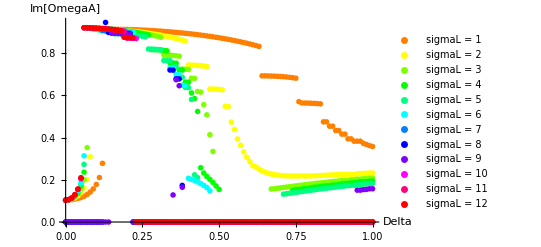

```mathematica
(*Assuming omegaValues,deltaValues,and rValues are already defined*)(*Create a list of data for each r value*)data=Table[Transpose[{deltaValues,Abs[Im[omegaValues[[i]]]]}],{i,Length[sigmaLValues]}];

(*Create a list of plot styles for each r value*)
plotStyles=Table[{Hue[i/Length[sigmaLValues]],PointSize[0.01]},{i,Length[sigmaLValues]}];

(*Create the plot*)
ListPlot[data,PlotStyle->plotStyles,Joined->False,PlotRange->All,AxesLabel->{"Delta","Im[OmegaA]"},PlotLegends->(StringJoin["sigmaL = ",ToString[#]]&/@sigmaLValues)]
```

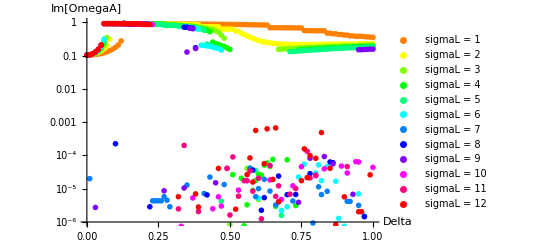

```mathematica
(*Assuming omegaValues,deltaValues,and rValues are already defined*)(*Create a list of data for each r value*)data=Table[Transpose[{deltaValues,Abs[Im[omegaValues[[i]]]]}],{i,Length[sigmaLValues]}];

(*Create a list of plot styles for each r value*)
plotStyles=Table[{Hue[i/Length[sigmaLValues]],PointSize[0.01]},{i,Length[sigmaLValues]}];

(*Create the plot*)
ListLogPlot[data,PlotStyle->plotStyles,Joined->False,PlotRange->{All,{10^-6,1}},(*Set the y-axis range from 10^-6 to 1*)AxesLabel->{"Delta","Im[OmegaA]"},PlotLegends->(StringJoin["sigmaL = ",ToString[#]]&/@sigmaLValues)]
```

```mathematica
(*Assuming omegaValues,deltaValues,and rValues are already defined*)(*Create a list of data for each r value*)data=Table[Transpose[{deltaValues,Abs[Im[omegaValues[[i]]]]}],{i,Length[sigmaLValues]}];

(*Create a list of plot styles for each r value*)
plotStyles=Table[{Hue[i/Length[sigmaLValues]],PointSize[0.01]},{i,Length[sigmaLValues]}];

(*Create the interactive plot*)
Manipulate[ListPlot[data[[i]],PlotStyle->plotStyles[[i]],Joined->False,PlotRange->All,AxesLabel->{"Delta","Im[OmegaA]"},PlotLabel->StringJoin["sigmaL = ",ToString[sigmaLValues[[i]]]]],{{i,1,"sigmaL value"},1,Length[sigmaLValues],1}]
```

Part::partd: Part specification data⟦4⟧ is longer than depth of object.

Part::partd: Part specification plotStyles⟦4⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 4 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: data⟦4⟧ is not a list of numbers or pairs of numbers.

```mathematica
(*Assuming omegaValues,deltaValues,and rValues are already defined*)(*Create a list of data for each r value*)data=Table[Transpose[{deltaValues,Abs[Im[omegaValues[[i]]]]}],{i,Length[sigmaLValues]}];

(*Create a list of plot styles for each r value*)
plotStyles=Table[{Hue[i/Length[sigmaLValues]],PointSize[0.01]},{i,Length[sigmaLValues]}];

(*Create a list of plots for each r value*)
plots=Table[ListPlot[data[[i]],PlotStyle->plotStyles[[i]],Joined->False,PlotRange->{0,1},AxesLabel->{"Delta","Im[OmegaA]"},PlotLabel->StringJoin["sigmaL = ",ToString[sigmaLValues[[i]]]]],{i,Length[sigmaLValues]}];

(*Export the animation as a GIF*)
Export["animation.gif",plots,"DisplayDurations"->0.3]
```

animation.gif

```mathematica
SystemOpen["animation.gif"]
```

```mathematica
SystemOpen["animation.gif"]
```

```mathematica
data=Table[Transpose[{deltaValues,Abs[Im[omegaValues[[i]]]]}],{i,Length[sigmaLValues]}];

(*Create a list of plot styles for each r value*)
plotStyles=Table[{Hue[i/Length[sigmaLValues]],PointSize[0.01]},{i,Length[sigmaLValues]}];

(*Create the interactive plot*)
Manipulate[ListLogPlot[data[[i]],PlotStyle->plotStyles[[i]],Joined->False,PlotRange->{All,{10^-6,1}},AxesLabel->{"Delta","Im[OmegaA]"},PlotLabel->StringJoin["sigmaL = ",ToString[sigmaLValues[[i]]]]],{{i,1,"sigmaL value"},1,Length[sigmaLValues],1}]
```

Part::partd: Part specification data⟦10⟧ is longer than depth of object.

Part::partd: Part specification plotStyles⟦10⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 10 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLogPlot::lpn: data⟦10⟧ is not a list of numbers or pairs of numbers.

```mathematica
(*Assuming your dataset is named'dataset'*)Export["C:\\Users\\Semed\\OneDrive\\Desktop\\New folder/file.csv",dataset]
```

C:\Users\Semed\OneDrive\Desktop\New folder/file.csv

```mathematica
SystemOpen["C:\\Users\\Semed\\OneDrive\\Desktop\\New folder/file.xlsx"]
```

```mathematica
data=Table[Transpose[{deltaValues,Abs[Re[omegaValues[[i]]]]}],{i,Length[sigmaLValues]}];

(*Create a list of plot styles for each r value*)
plotStyles=Table[{Hue[i/Length[sigmaLValues]],PointSize[0.01]},{i,Length[sigmaLValues]}];

(*Create the interactive plot*)
Manipulate[ListLogPlot[data[[i]],PlotStyle->plotStyles[[i]],Joined->False,PlotRange->{All,{10^-6,1}},AxesLabel->{"Delta","Re[OmegaA]"},PlotLabel->StringJoin["sigmaL = ",ToString[sigmaLValues[[i]]]]],{{i,1,"sigmaL value"},1,Length[sigmaLValues],1}]
```

Part::partd: Part specification data⟦12⟧ is longer than depth of object.

Part::partd: Part specification plotStyles⟦12⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 12 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLogPlot::lpn: data⟦12⟧ is not a list of numbers or pairs of numbers.